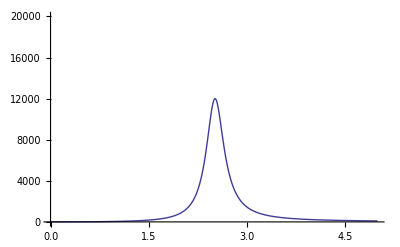

```mathematica
ReZ [k_, L_, R_, f_, C_] := (k^2*L^2*R*(2π*f)^2)/(L^2*C^2*R^2*(2π*f)^4+(L^2-2*L*C*R^2)*(2π*f)^2+R^2);
Plot[ReZ[1, 100*10^-6,12*10^3,x*10^6,40*10^-12], {x, 0, 5}, PlotRange-> {0, 20000}]
```